# Quark–antiquark annihilation with graviton emission

q̄(p₁) + q(p₂) → h(p₃) + A(p₄). One fundamental Dirac flavour has arbitrary mass m. This tree example keeps D and N symbolic and uses FeynGravSimplify with FORM for Lorentz, Dirac and colour algebra. Start in a fresh kernel and evaluate from top to bottom. No spin or colour average is taken.

## 1. Load FeynGrav and the model

```mathematica
$LoadAddOns={"FeynArts"};<<"FeynGrav`";
```

```mathematica
model="GR-SU-N-Yang-Mills";InitializeModel[model,GenericModel->model];SetOptions[FeynGravSimplify,Method->"FORM",FORMThreads->1,LoopMomenta->{},TensorDecomposition->False];
```

F[1] is the quark and -F[1] its antiquark; T[1] is the graviton and V[1] the gluon. The unchanged model name now includes one quark flavour. The gravitational ghost uses S[1]; U[1] remains the Yang–Mills ghost.

## 2. Construct and display the four diagrams

```mathematica
topologies=CreateTopologies[0,2->2,Adjacencies->{3,4,5,6}];insertions=InsertFields[topologies,{-F[1],F[1]}->{T[1],V[1]},Model->model,GenericModel->model,InsertionLevel->{Classes}];
```

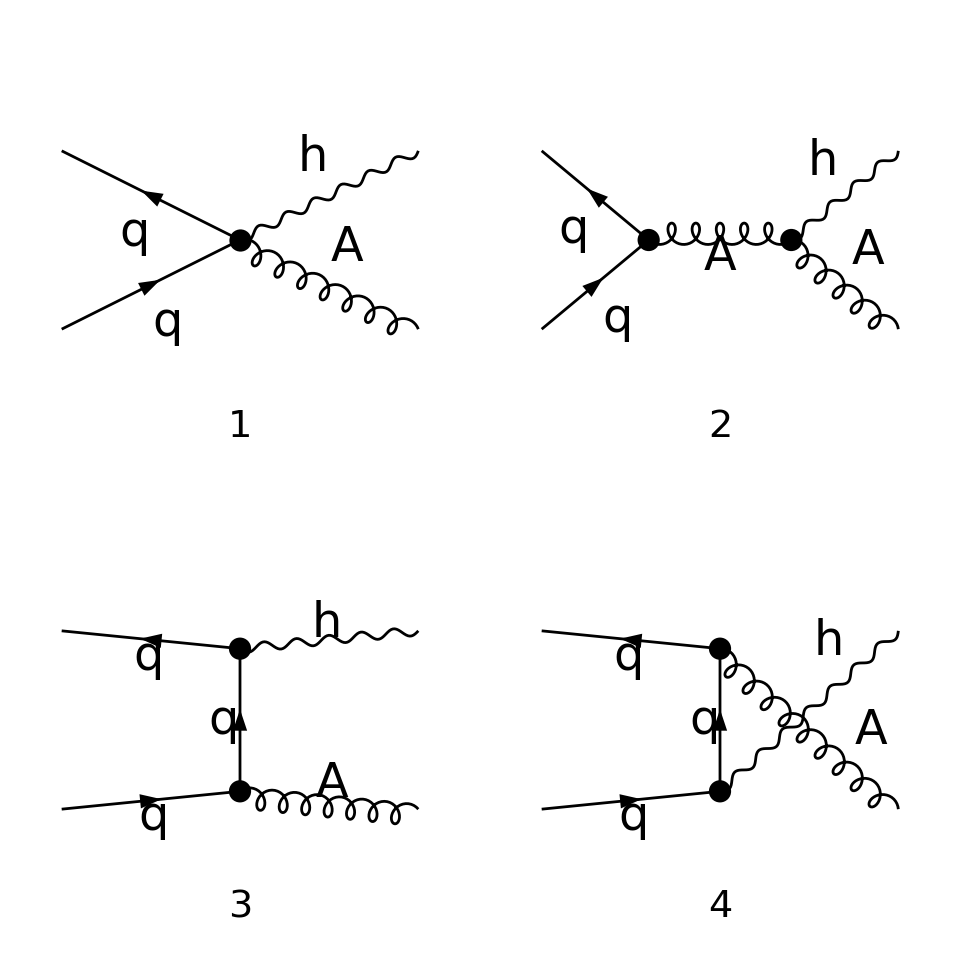

```mathematica
Paint[insertions,ColumnsXRows->{2,2},Numbering->Simple,SheetHeader->"Quark annihilation with graviton emission",AutoEdit->False,DisplayFunction->Function[sheet,diagramSheets=Render[sheet,ImageSize->{960,960}]]];Column[diagramSheets]
```

The diagrams are the hq̄qA contact, an s-channel gluon, and two quark exchanges. FeynArts supplies their relative signs and tree weights; no additional symmetry factors are inserted.

## 3. Fix on-shell kinematics

```mathematica
FCClearScalarProducts[];SetMandelstam[s,t,u,p1,p2,-p3,-p4,m,m,0,0];onShell[expr_]:=ExpandScalarProduct[DiracGammaExpand[MomentumExpand[FCI[expr]]/.Momentum[p4,D]->Momentum[p1+p2-p3,D]]]/.u->2 m^2-s-t;
```

Outgoing states use conjugated polarisation vectors, Polarization[p, -I]. The graviton tensor is a product of two transverse null vectors, which is traceless. These conditions select physical external states without setting D = 4. The last scalar-product assignment combines gluon transversality with momentum conservation.

```mathematica
Pair[Momentum[p3,D],Momentum[Polarization[p3,-ⅈ],D]]=0;Pair[Momentum[Polarization[p3,-ⅈ],D],Momentum[Polarization[p3,-ⅈ],D]]=0;Pair[Momentum[p4,D],Momentum[Polarization[p4,-ⅈ],D]]=0;Pair[Momentum[p3,D],Momentum[Polarization[p4,-ⅈ],D]]=Pair[Momentum[p1,D],Momentum[Polarization[p4,-ⅈ],D]]+Pair[Momentum[p2,D],Momentum[Polarization[p4,-ⅈ],D]];
```

## 4. Calculate and present the amplitude

Truncated -> True leaves the ordered Dirac matrix and external Lorentz indices open. In these four diagrams every internal colour index forms a paired contraction, so DropSumOver -> True lets FORM perform the corresponding Einstein sums. This choice has been checked for this process and should not be copied blindly to other amplitudes.

```mathematica
raw=CreateFeynAmp[insertions,Truncated->True,MomentumConservation->True,PreFactor->1];diagrams=FCFAConvert[raw,IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},ChangeDimension->D,LorentzIndexNames->{μ,ν,ρ,α,β,γ,δ},List->True,SMP->False,Contract->False,DropSumOver->True]/.{QuarkMass->m,YangMillsCoupling->gs};amplitudeTensor=FeynAmpDenominatorExplicit[Total[diagrams]];
```

Check that the four required diagrams were constructed. The result should be True.

```mathematica
Length[diagrams]===4
```

True

```mathematica
matrixElement=FeynGravSimplify[onShell[amplitudeTensor FVD[Polarization[p3,-ⅈ],μ] FVD[Polarization[p3,-ⅈ],ν] FVD[Polarization[p4,-ⅈ],ρ]]];
```

The diagram result contains i times the scattering amplitude. Divide by i and attach the incoming antiquark and quark spinors after the FORM calculation. FORM processes the open Dirac matrix, not the external spinors.

```mathematica
ℳ=DotSimplify[(SpinorVBarD[p1,m].matrixElement.SpinorUD[p2,m])/ⅈ]
```

-ⅈ (-(ⅈ gs m κ Spinor[-Momentum[p1,D],m,1].DiracGamma[Momentum[Polarization[p3,-ⅈ],D],D].DiracGamma[Momentum[Polarization[p4,-ⅈ],D],D].Spinor[Momentum[p2,D],m,1] Pair[Momentum[p1,D],Momentum[Polarization[p3,-ⅈ],D]] SUNTF[{SUNIndex[Glu4]},SUNFIndex[Col1],SUNFIndex[Col2]])/(2 (m^2-t))-(ⅈ gs κ Spinor[-Momentum[p1,D],m,1].DiracGamma[Momentum[Polarization[p3,-ⅈ],D],D].DiracGamma[Momentum[Polarization[p4,-ⅈ],D],D].DiracGamma[Momentum[p1,D],D].Spinor[Momentum[p2,D],m,1] Pair[Momentum[p1,D],Momentum[Polarization[p3,-ⅈ],D]] SUNTF[{SUNIndex[Glu4]},SUNFIndex[Col1],SUNFIndex[Col2]])/(2 (m^2-t))+(ⅈ gs κ Spinor[-Momentum[p1,D],m,1].DiracGamma[Momentum[Polarization[p3,-ⅈ],D],D].DiracGamma[Momentum[Polarization[p4,-ⅈ],D],D].DiracGamma[Momentum[p3,D],D].Spinor[Momentum[p2,D],m,1] Pair[Momentum[p1,D],Momentum[Polarization[p3,-ⅈ],D]] SUNTF[{SUNIndex[Glu4]},SUNFIndex[Col1],SUNFIndex[Col2]])/(2 (m^2-t))-(ⅈ gs κ Spinor[-Momentum[p1,D],m,1].DiracGamma[Momentum[Polarization[p4,-ⅈ],D],D].Spinor[Momentum[p2,D],m,1] Pair[Momentum[p1,D],Momentum[Polarization[p3,-ⅈ],D]]^2 SUNTF[{SUNIndex[Glu4]},SUNFIndex[Col1],SUNFIndex[Col2]])/s+(ⅈ gs κ Spinor[-Momentum[p1,D],m,1].DiracGamma[Momentum[Polarization[p3,-ⅈ],D],D].Spinor[Momentum[p2,D],m,1] Pair[Momentum[p1,D],Momentum[Polarization[p3,-ⅈ],D]] Pair[Momentum[p1,D],Momentum[Polarization[p4,-ⅈ],D]] SUNTF[{SUNIndex[Glu4]},SUNFIndex[Col1],SUNFIndex[Col2]])/(m^2-t)+(ⅈ gs m κ Spinor[-Momentum[p1,D],m,1].DiracGamma[Momentum[Polarization[p3,-ⅈ],D],D].DiracGamma[Momentum[Polarization[p4,-ⅈ],D],D].Spinor[Momentum[p2,D],m,1] Pair[Momentum[p2,D],Momentum[Polarization[p3,-ⅈ],D]] SUNTF[{SUNIndex[Glu4]},SUNFIndex[Col1],SUNFIndex[Col2]])/(2 (m^2-s-t))-(ⅈ gs κ Spinor[-Momentum[p1,D],m,1].DiracGamma[Momentum[Polarization[p3,-ⅈ],D],D].DiracGamma[Momentum[Polarization[p4,-ⅈ],D],D].DiracGamma[Momentum[p2,D],D].Spinor[Momentum[p2,D],m,1] Pair[Momentum[p2,D],Momentum[Polarization[p3,-ⅈ],D]] SUNTF[{SUNIndex[Glu4]},SUNFIndex[Col1],SUNFIndex[Col2]])/(2 (m^2-s-t))+(ⅈ gs κ Spinor[-Momentum[p1,D],m,1].DiracGamma[Momentum[Polarization[p3,-ⅈ],D],D].DiracGamma[Momentum[Polarization[p4,-ⅈ],D],D].DiracGamma[Momentum[p3,D],D].Spinor[Momentum[p2,D],m,1] Pair[Momentum[p2,D],Momentum[Polarization[p3,-ⅈ],D]] SUNTF[{SUNIndex[Glu4]},SUNFIndex[Col1],SUNFIndex[Col2]])/(2 (m^2-s-t))-(2 ⅈ gs κ Spinor[-Momentum[p1,D],m,1].DiracGamma[Momentum[Polarization[p4,-ⅈ],D],D].Spinor[Momentum[p2,D],m,1] Pair[Momentum[p1,D],Momentum[Polarization[p3,-ⅈ],D]] Pair[Momentum[p2,D],Momentum[Polarization[p3,-ⅈ],D]] SUNTF[{SUNIndex[Glu4]},SUNFIndex[Col1],SUNFIndex[Col2]])/s+(ⅈ gs (m^2-t) κ Spinor[-Momentum[p1,D],m,1].DiracGamma[Momentum[Polarization[p4,-ⅈ],D],D].Spinor[Momentum[p2,D],m,1] Pair[Momentum[p2,D],Momentum[Polarization[p3,-ⅈ],D]]^2 SUNTF[{SUNIndex[Glu4]},SUNFIndex[Col1],SUNFIndex[Col2]])/(s (-m^2+s+t))+(ⅈ gs (m^2-s-t) κ Spinor[-Momentum[p1,D],m,1].DiracGamma[Momentum[Polarization[p3,-ⅈ],D],D].Spinor[Momentum[p2,D],m,1] Pair[Momentum[p1,D],Momentum[Polarization[p3,-ⅈ],D]] (Pair[Momentum[p1,D],Momentum[Polarization[p4,-ⅈ],D]]+Pair[Momentum[p2,D],Momentum[Polarization[p4,-ⅈ],D]]) SUNTF[{SUNIndex[Glu4]},SUNFIndex[Col1],SUNFIndex[Col2]])/(s (m^2-t))+(ⅈ gs κ Spinor[-Momentum[p1,D],m,1].DiracGamma[Momentum[Polarization[p3,-ⅈ],D],D].Spinor[Momentum[p2,D],m,1] Pair[Momentum[p2,D],Momentum[Polarization[p3,-ⅈ],D]] (Pair[Momentum[p1,D],Momentum[Polarization[p4,-ⅈ],D]]+Pair[Momentum[p2,D],Momentum[Polarization[p4,-ⅈ],D]]) SUNTF[{SUNIndex[Glu4]},SUNFIndex[Col1],SUNFIndex[Col2]])/s-(ⅈ gs κ Spinor[-Momentum[p1,D],m,1].DiracGamma[Momentum[p3,D],D].Spinor[Momentum[p2,D],m,1] Pair[Momentum[p1,D],Momentum[Polarization[p3,-ⅈ],D]] Pair[Momentum[Polarization[p3,-ⅈ],D],Momentum[Polarization[p4,-ⅈ],D]] SUNTF[{SUNIndex[Glu4]},SUNFIndex[Col1],SUNFIndex[Col2]])/s-(ⅈ gs m κ Spinor[-Momentum[p1,D],m,1].Spinor[Momentum[p2,D],m,1] Pair[Momentum[p2,D],Momentum[Polarization[p3,-ⅈ],D]] Pair[Momentum[Polarization[p3,-ⅈ],D],Momentum[Polarization[p4,-ⅈ],D]] SUNTF[{SUNIndex[Glu4]},SUNFIndex[Col1],SUNFIndex[Col2]])/(m^2-s-t)+(ⅈ gs κ Spinor[-Momentum[p1,D],m,1].DiracGamma[Momentum[p2,D],D].Spinor[Momentum[p2,D],m,1] Pair[Momentum[p2,D],Momentum[Polarization[p3,-ⅈ],D]] Pair[Momentum[Polarization[p3,-ⅈ],D],Momentum[Polarization[p4,-ⅈ],D]] SUNTF[{SUNIndex[Glu4]},SUNFIndex[Col1],SUNFIndex[Col2]])/(m^2-s-t)+(ⅈ gs (m^2-t) κ Spinor[-Momentum[p1,D],m,1].DiracGamma[Momentum[p3,D],D].Spinor[Momentum[p2,D],m,1] Pair[Momentum[p2,D],Momentum[Polarization[p3,-ⅈ],D]] Pair[Momentum[Polarization[p3,-ⅈ],D],Momentum[Polarization[p4,-ⅈ],D]] SUNTF[{SUNIndex[Glu4]},SUNFIndex[Col1],SUNFIndex[Col2]])/(s (-m^2+s+t)))

## 5. Check the coupling limits and both gauge symmetries

Turning off gravity must remove this graviton-emission amplitude. The result should be True.

```mathematica
(matrixElement/.κ->0)===0
```

True

Turning off the Yang–Mills coupling must also remove this process. The result should be True.

```mathematica
(matrixElement/.gs->0)===0
```

True

For the gluon Ward identity, replace its polarisation by p₄. The factors (slash p₁ − m) and (slash p₂ + m) impose the incoming antiquark and quark Dirac equations while keeping all spin states. The resulting matrix must vanish. The result should be True.

```mathematica
gluonResidual=onShell[FeynGravSimplify[(GSD[p1]-m).onShell[amplitudeTensor FVD[Polarization[p3,-ⅈ],μ] FVD[Polarization[p3,-ⅈ],ν] FVD[p4,ρ]].(GSD[p2]+m)]];Expand[Together[gluonResidual]]===0
```

True

For the gravitational Ward identity, replace the graviton tensor by p₃ᵐᵘ ξⁿᵘ + ξᵐᵘ p₃ⁿᵘ. The vector ξ is arbitrary: no transversality or null condition is imposed on it. Keep the gluon physical and impose the same external Dirac equations. The result should be True.

```mathematica
gravitonResidual=onShell[FeynGravSimplify[(GSD[p1]-m).onShell[amplitudeTensor (FVD[p3,μ] FVD[ξ,ν]+FVD[ξ,μ] FVD[p3,ν]) FVD[Polarization[p4,-ⅈ],ρ]].(GSD[p2]+m)]];Expand[Together[gravitonResidual]]===0
```

True

These checks concern this complete tree amplitude. They do not establish loop identities, renormalisation, or every higher-point process. The model cutoff is κ262 per vertex, not a restriction on the total order of every diagram.